# Computation Explorations with physical quantities and other areas of physics

Peter Cullen Burbery

I decided to take a look at various neat examples for functions for physical quantities. I am creating a computational exploration with physical quantities. I focus on using graphs in particular.

## Physical Quantity Analysis

Find all physical quantities with the same dimensions as ohms:

Use the resource function PhysicalQuantityLookup:

```mathematica
PersistResourceFunction["PhysicalQuantityLookup"]
```

Success[…]

```mathematica
PhysicalQuantityLookup["Ohms"]
```

{AC resistance,DC resistance,electric resistance,internal winding resistance,resistive load,electric surface resistance,cable impedance,characteristic electric impedance,electric alternating current resistance,electric differential resistance,electric impedance,electric impedance modulus,electric mutual resistance,electric reactance,impedance load,inductor impedance,magnetic inductance rate,magnetic memristance,magnetoelectric coefficient dE/dH,transformer sensitivity}

Look for physical quantities that cover a quantity:

```mathematica
PhysicalQuantityLookup[Quantity[, ("Meters")^4]]
```

{area moment of inertia x,area moment of inertia y,axial area moment of inertia,planar area moment of inertia,polar area moment of inertia,product area moment of inertia,transformer area product}

Look up physical quantities with the dimensions of power:

```mathematica
PhysicalQuantityLookup[Quantity[, "Terawatts"]]
```

{power,energy flux,electric power,energy flow rate,heat flow rate,real power,active power,battery energy self-discharge rate,bolometric luminosity,tonnage rating,dietary energy intake rate,electric apparent power,electric complex power,electric non-active power,electric reactive power,energy consumption rate,energy production rate,input power,Larmor power,livestock carrying capacity,luminosity,mechanical power,output power,radiant power,solar panel electric output power,solar power,sound power,stellar luminosity,tidal power,vacuum pump leakage rate,wave power,wind power}

I first need to store my resource function PhysicalQuantityData:

```mathematica
PersistResourceFunction["PhysicalQuantityData"]
```

Success[…]

Group physical quantities by their base physical quantity:

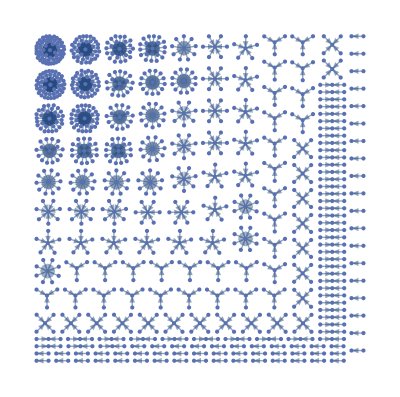

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by  SI unit:

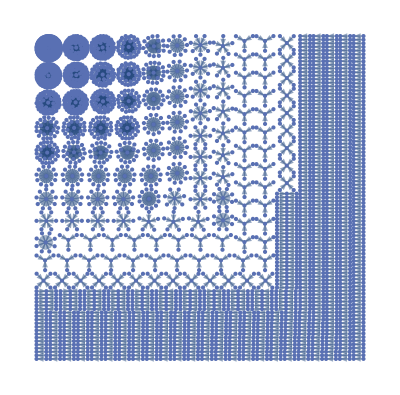

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by SI base unit:

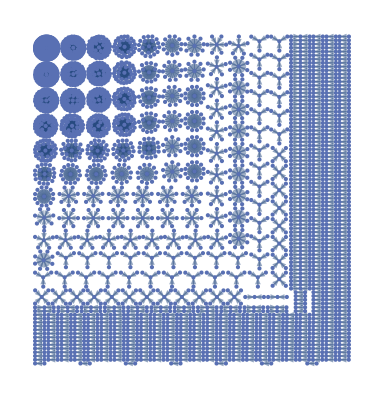

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIBaseUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by total absolute dimension:

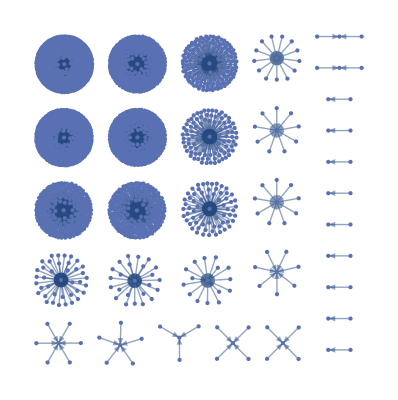

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],Total[Abs[#[[All,-1]]]]&/@EntityValue[PhysicalQuantityData[],"Dimensions"]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by total dimensions:

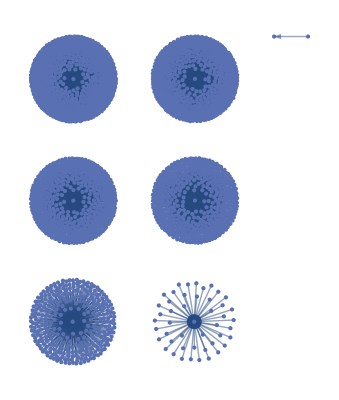

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],Length/@EntityValue[PhysicalQuantityData[],"Dimensions"]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

This comes from a neat example for the documentation for PhysicalQuantity.

Visualize the dimensionality of physical quantities based on the standard dimensions:

```mathematica
dimensions={"LengthUnit","TimeUnit","AngleUnit","MassUnit","PhotonUnit","TemperatureDifferenceUnit","AmountUnit","TemperatureUnit","ElectricCurrentUnit","LuminousIntensityUnit","InformationUnit"};
```

Collect all physical quantities containing only those dimensions:

```mathematica
DimensionData=EntityValue[EntityClass["PhysicalQuantity","Dimensions"->(ContainsOnly[#[[All,1]],dimensions]&)],{"CanonicalName","Dimensions"}];
```

Convert dimension lists to vectors:

```mathematica
DimensionVector//ClearAll
DimensionVector[dims_]:=Lookup[Rule@@@dims,#,0]&/@dimensions
```

Visualize as a feature space plot:

```mathematica
FeatureSpacePlot[Callout[DimensionVector[#2],#1]&@@@DimensionData,LabelingFunction->None,ImageSize->Full]
```

-Graphics-

## Formula Data examples

Find all formulas that contain both the speed of light and Planck's constant as parameters:

```mathematica
Grid[{#,FormulaData[#]}&/@Select[FormulaData[],MemberQ[FormulaData[#],"SpeedOfLight",∞]&&MemberQ[FormulaData[#],"PlanckConstant",∞]&],Dividers->Center,Alignment->Left]
```

ComptonWavelength | λ_C Wavelength==(h/c)/(m Mass)
{BraggsLaw,Energy} | {n MultiplicativeConstants λ Wavelength==2 d Distance Sin[θ Angle],λ Wavelength==(h c)/(E Energy)}
{ComptonShift,Wavelengths} | -λ Wavelength+λ' LightWavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{ComptonShift,WavelengthShift} | Δλ Wavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{PhotonEnergy,Wavelength} | E Energy==(h c)/(λ Wavelength)
{PhotonMomentum,Frequency} | p Momentum==( h/c) ν Frequency
{PhotonWavelength,Energy} | E Energy==(h c)/(λ Wavelength)
{PlanckRadiationLaw,Frequency} | L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))
{PlanckRadiationLaw,Wavelength} | L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
{ThermalDeBroglieWavelength,MasslessParticle} | Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature)
{DeBroglieRelationsRelativistic,Frequency,Momentum} | f Frequency==(1 /h) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2))
{DeBroglieRelationsRelativistic,Frequency,Velocity} | f Frequency==(( c^2/h) m Mass)/(√(1+(-1 /c^2) (v Speed)^2))
{DeBroglieRelationsRelativistic,Wavelength,KineticEnergy} | λ Wavelength==(h c)/(√((K Energy)^2+(2 c^2) K Energy m Mass))
{DeBroglieRelationsRelativistic,Wavelength,Velocity} | λ Wavelength==(( h) √(1+(-1 /c^2) (v Speed)^2))/(m Mass v Speed)

I am including a neat example of exploring fundamental physics formulas:

Select all formulas that contain Planck's constant, speed of light, or gravitational constant as a parameter:

```mathematica
chGFormulas = Select[(Column[Flatten@{#, FormulaData[#],FormulaData[#,"QuantityVariableTable"]}]& /@ FormulaData[]) /. 
Quantity[q_,"ReducedPlanckConstant"]:> Quantity[q/.None->1/(2Pi),"PlanckConstant"],        
                                           MemberQ[#, "PlanckConstant"|"SpeedOfLight"|"GravitationalConstant", ∞]&];
```

Construct a network of formulas based on related physical quantities:

```mathematica
chGformulaNetwork = Select[{UndirectedEdge[#1,#2],Length[Intersection @@(Union[Last/@Cases[#,_QuantityVariable, ∞]]& /@ {#1, #2})]}&@@@ Subsets[chGFormulas, {2}],Last[#]>0&];
```

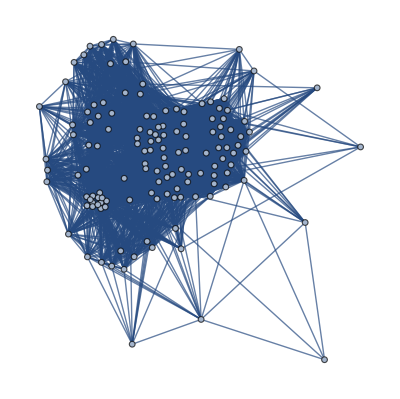

```mathematica
Graph[First /@ chGformulaNetwork,EdgeWeight->1/(Last /@ chGformulaNetwork),
       GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},
       VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Analyze the structure of the graph:

```mathematica
CommunityGraphPlot[Graph[First /@ chGformulaNetwork,EdgeWeight->1/(Last /@ chGformulaNetwork),
       GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},
       VertexLabels->Placed["Name",Tooltip],ImageSize->Full]]
```

-Graphics-

## NondimensionalizationTransform examples

Transform Coulomb's law and Newton's law of gravitation using different sets of natural units:

```mathematica
naturalunits={"PlanckUnits","HartreeAtomicUnits","RydbergAtomicUnits","LorentzHeavisideNaturalUnits","GaussianNaturalUnits"};
```

```mathematica
cleq=First@FormulaData["CoulombsLaw"]
```

F Force==((1/(4 π) /ε_0) Q_1 ElectricCharge Q_2 ElectricCharge)/(r Distance)^2

```mathematica
nlogeq=FormulaData["NewtonsLawOfUniversalGravitation"]
```

F Force==(( G) m_1 Mass m_2 Mass)/(r Distance)^2

```mathematica
coulomb=NondimensionalizationTransform[cleq,{"F" "Force",Subscript["Q", 1] "ElectricCharge", Subscript["Q", 2] "ElectricCharge","r" "Distance"},{f,q1,q2,ρ},UnitSystem->#]&/@naturalunits;
gravity=NondimensionalizationTransform[nlogeq,{"F" "Force", Subscript["m", 1] "Mass", Subscript["m", 2] "Mass","r" "Distance"},{f,m1,m2,ρ},UnitSystem->#]&/@naturalunits;
```

Compare how the formulas look under different natural unit systems:

```mathematica
Grid[Prepend[Transpose[{naturalunits,gravity,coulomb}],{"unit system","gravitational force","electrostatic force"}],Dividers->Center]
```

unit system | gravitational force | electrostatic force
PlanckUnits | f==(m1 m2)/ρ^2 | f==(q1 q2)/ρ^2
HartreeAtomicUnits | f (1/(4 π) e^2/(m_e^2 ε_0 G))==(m1 m2)/ρ^2 | f==(q1 q2)/ρ^2
RydbergAtomicUnits | f (1/(8 π) e^2/(m_e^2 ε_0 G))==(m1 m2)/ρ^2 | 1024 f==(q1 q2)/ρ^2
LorentzHeavisideNaturalUnits | 1.491×10^56 f==(m1 m2)/ρ^2 | f (16 π^2 α ε_0 ℏ c/e^2)==(q1 q2)/ρ^2
GaussianNaturalUnits | 1.491×10^56 f==(m1 m2)/ρ^2 | f (4 π α ε_0 ℏ c/e^2)==(q1 q2)/ρ^2

## Physical Constant examples

Visualize the characteristic length and mass scales for various objects (cf. https://arxiv.org/pdf/1910.00481https://arxiv.org/pdf/1910.00481):

```mathematica
data={
"universe"->{"UniverseRadius","UniverseMass"},
"Planck"->{"PlanckLength","PlanckMass"},
"CQ point"->{"CosmologicalQuantumPointLength","CosmologicalQuantumPointMass"},
"Earth"->{"EarthMeanRadius","EarthMass"},
"Sun"->{"SolarRadius","SolarMass"},
"electron"->{"ClassicalElectronRadius","ElectronMass"},
"proton"->{"ClassicalProtonRadius","ProtonMass"}
};
```

Compute the common logarithms for the magnitudes of the preceding length/radius pairs:

```mathematica
pts=Append[Map[Log10[QuantityMagnitude[UnitConvert[Entity["PhysicalConstant",#]["Value"],"SIBase"]]]&,data[[All,2]],{2}],{0,0}];
```

```mathematica
labels=Append[data[[All,1]],"human"];
```

Plot the points in length-mass space. where the red line marks the quantum mechanical boundary, the green line marks the black hole boundary, the light blue line marks the boundary from the cosmological density, and the point of intersection of the black hole and cosmological lines is termed the cosmological-quantum (CQ) point:

```mathematica
Show[{
Graphics[{AbsoluteThickness[2],Transpose[{{Green,Hue[.5],Red},InfiniteLine/@Subsets[Take[pts,3],{2}]}]
}],
ListPlot[Thread[pts->labels],]
},]
```

-Graphics-

## Dimensional Combinations examples

Explore the possible dimensionless combinations of electromagnetic physical quantities:

```mathematica
DimensionalCombinations[{
  QuantityVariable["Q", "ElectricCharge"],
  QuantityVariable["V", "ElectricPotential"], QuantityVariable["I", "ElectricCurrent"], QuantityVariable["R", "ElectricResistance"],
  QuantityVariable["C", "ElectricCapacitance"], QuantityVariable["L", "MagneticInductance"],
  QuantityVariable["M", "MagneticMemristance"], QuantityVariable["Φ", "MagneticFlux"]},
 GeneratedParameters -> None]
```

{(M MagneticMemristance)/(R ElectricResistance),(Q ElectricCharge)/(C ElectricCapacitance V ElectricPotential),(Φ MagneticFlux)/(Q ElectricCharge R ElectricResistance),(Φ MagneticFlux)/(M MagneticMemristance Q ElectricCharge),(I ElectricCurrent R ElectricResistance)/(V ElectricPotential),(I ElectricCurrent M MagneticMemristance)/(V ElectricPotential),(Φ MagneticFlux)/(I ElectricCurrent L MagneticInductance),(L MagneticInductance)/(C ElectricCapacitance (R ElectricResistance)^2),(C ElectricCapacitance (M MagneticMemristance)^2)/(L MagneticInductance),((I ElectricCurrent)^2 L MagneticInductance)/(Q ElectricCharge V ElectricPotential),(I ElectricCurrent Φ MagneticFlux)/(Q ElectricCharge V ElectricPotential),(L MagneticInductance V ElectricPotential)/(Q ElectricCharge (R ElectricResistance)^2),((M MagneticMemristance)^2 Q ElectricCharge)/(L MagneticInductance V ElectricPotential),(Φ MagneticFlux)^2/(L MagneticInductance Q ElectricCharge V ElectricPotential),(C ElectricCapacitance I ElectricCurrent R ElectricResistance)/(Q ElectricCharge),(I ElectricCurrent L MagneticInductance)/(Q ElectricCharge R ElectricResistance),(C ElectricCapacitance (I ElectricCurrent)^2 L MagneticInductance)/(Q ElectricCharge)^2,(C ElectricCapacitance I ElectricCurrent M MagneticMemristance)/(Q ElectricCharge),(C ElectricCapacitance I ElectricCurrent Φ MagneticFlux)/(Q ElectricCharge)^2,(I ElectricCurrent L MagneticInductance)/(M MagneticMemristance Q ElectricCharge),(C ElectricCapacitance (Φ MagneticFlux)^2)/(L MagneticInductance (Q ElectricCharge)^2),((I ElectricCurrent)^2 L MagneticInductance)/(C ElectricCapacitance (V ElectricPotential)^2),(I ElectricCurrent Φ MagneticFlux)/(C ElectricCapacitance (V ElectricPotential)^2),(Φ MagneticFlux)/(C ElectricCapacitance R ElectricResistance V ElectricPotential),(R ElectricResistance Φ MagneticFlux)/(L MagneticInductance V ElectricPotential),(Φ MagneticFlux)^2/(C ElectricCapacitance L MagneticInductance (V ElectricPotential)^2),(Φ MagneticFlux)/(C ElectricCapacitance M MagneticMemristance V ElectricPotential),(M MagneticMemristance Φ MagneticFlux)/(L MagneticInductance V ElectricPotential),(C ElectricCapacitance I ElectricCurrent (R ElectricResistance)^2)/(Φ MagneticFlux),(C ElectricCapacitance I ElectricCurrent (M MagneticMemristance)^2)/(Φ MagneticFlux)}

Derive the factor for the fine structure constant from physical quantities:

```mathematica
sol=DimensionalCombinations[{},
 IncludeQuantities -> {
  Quantity["SpeedOfLight"], Quantity["PlanckConstant"] , Quantity["ElectricConstant"] ,
  Quantity["ElementaryCharge"]
  },
 GeneratedParameters -> None]
```

{1 ε_0 h c/e^2}

```mathematica
UnitConvert[sol[[1]],"SIBase"]^2/Quantity["FineStructureConstant"]
```

4694.71626 /α